```mathematica
(*Set as ...PathtoGithubFolder/DataFiles *)
dire="~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles";
SetDirectory[dire];
Get[dire<>"/init.m"]
```

```mathematica
(*Leo T data from Faerman et al. 2013 model*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/LeoT_profiles_Faerman13.dat"];
(*Columns are: r (kpc) n_DM (cm^-3) n_H (cm^-3) n_e (cm^-3) n_HI (cm^-3)*)
data=DeleteDuplicatesBy[data,First];
rl= data[[All,1]];
dml=Interpolation[Transpose[{data[[All,1]],mp/mgev data[[All,2]]}]];
nhl=Interpolation[Transpose[{data[[All,1]],data[[All,3]]}]];
nel=Interpolation[Transpose[{data[[All,1]],data[[All,4]]}]];
nh1l=Interpolation[Transpose[{data[[All,1]],data[[All,5]]}]];
```

InterpolatingFunction::dmval: Input value {0.0000143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

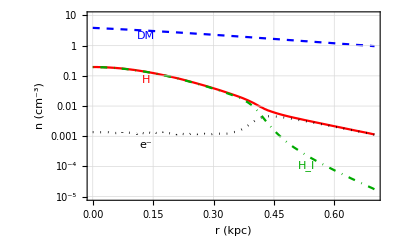

```mathematica
Show[LogPlot[{dml[r],nhl[r],nel[r],nh1l[r]},{r,0,0.7},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.6,FrameLabel->{"r (kpc)","n (cm^-3)"},PlotRange->{{0,0.7},{10^-5,10}},PlotStyle->{{Blue,Dashed},{Red},{Black,Dotted},{Darker[Green],DotDashed},{RGBColor[0.363898, 0.618501, 0.782349],Dashed},{RGBColor[0.647624, 0.37816, 0.614037],DotDashed}}(*PlotRange->{{0.002,10},{4 10^-25,10^-20}},*)],Graphics[{Text[Style["DM",Blue],Scaled[{0.2,0.87}],{0,0},Automatic,{1,0}],Text[Style["H",Red],Scaled[{0.2,0.64}],{0,0},Automatic,{1,0}],Text[Style["e^-",Black],Scaled[{0.2,0.295}],{0,0},Automatic,{1,0}],Text[Style["H_I",Darker[Green]],Scaled[{0.75,0.185}],{0,0},Automatic,{1,0}]}]]
```

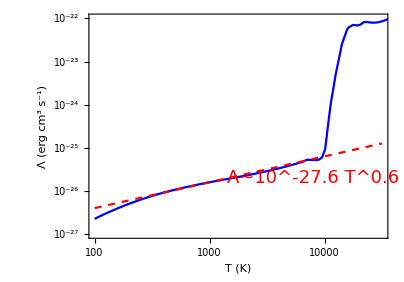

```mathematica
(*Cooling Function*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/CoolingFunc_Grackle.dat"];
Show[ListLogLogPlot[{data},FrameStyle->Black,Joined->True,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.7,FrameLabel->{"T (K)","Λ (erg cm^3 s^-1)"},PlotStyle->{Blue},PlotRange->{{100,10^4.5},{10^-27,10^-22}}],LogLogPlot[10^-25.8(t/1000)^0.6,{t,100,10^4.5},PlotStyle->{Red,Dashed}],Graphics[{Text[Style["Λ~10^-27.6 T^0.6",Red,18],Scaled[{0.75,0.27}],{0,0},Automatic,{1,0.2}]}]]
```

```mathematica
Table[uldp[i]=Import["ULDP/"<>ToString[i]<>".dat"],{i,8}];
```

```mathematica
temp= Join[Drop[uldp[1],-1],uldp[2]];
epInt=Interpolation[Transpose[{Log10[temp[[All,1]]],Log[temp[[All,2]]]}]];
dashing=Table[{{10.^i,Exp[epInt[i]]},{10.^(i+1),Exp[epInt[i]] 10^10}},{i,-20.1,-7.1,0.8}];
```

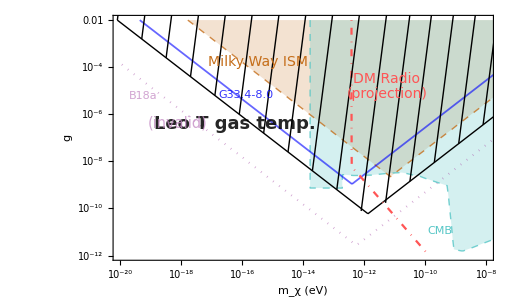

```mathematica
Show[ListLogLogPlot[{uldp[1],uldp[2],uldp[3],uldp[4],uldp[5],uldp[6],uldp[7],uldp[8]},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,Filling->{3->{Top,RGBColor[0.772079, 0.431554, 0.102387, 0.2]},5->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.25]}},AspectRatio->0.6,FrameLabel->{Style["m_χ (eV)",18],Style["g",18]},PlotStyle->{{Black,Thick},{Black,Thick},{RGBColor[0.772079, 0.431554, 0.102387, 0.8],Dashed,Thin},{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.6],Dotted,Thickness->0.003},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0, 0, 1, 0.6],Thickness->0.0025},{RGBColor[0, 0, 1, 0.6],Thickness->0.0025},{RGBColor[1, Rational[1, 3], Rational[1, 3]],DotDashed}},GridLinesStyle->LightGray,PlotRange->{{10^-20,10^-8},{10^-12,10^-2}}],Graphics[{Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.32,0.555}],{0,0},Automatic,{1,-0.7}],
Text[Style["Milky Way ISM",RGBColor[0.772079, 0.431554, 0.102387],14],Scaled[{0.38,0.81}],{0,0},Automatic,{1,-0.7}],
Text[Style["DM Radio",RGBColor[1, Rational[1, 3], Rational[1, 3]],14],Scaled[{0.72,0.74}],{0,0},Automatic,{1,0}],
Text[Style["(projection)",RGBColor[1, Rational[1, 3], Rational[1, 3]],14],Scaled[{0.72,0.68}],{0,0},Automatic,{1,0}],
Text[Style["G33.4-8.0",RGBColor[0, 0, 0.98, 0.8]],Scaled[{0.35,0.675}],{0,0},Automatic,{1,-0.75}],
Text[Style["B18a",RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778, 0.8]],Scaled[{0.08,0.67}],{0,0},Automatic,{1,-0.75}],
Text[Style["(invalid)",RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778, 0.8],14.5],Scaled[{0.17,0.56}],{0,0},Automatic,{1,-0.75}],
Text[Style["CMB",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]]],Scaled[{0.86,0.12}],{0,0},Automatic,{1,0}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin(*,Thickness->0.00005*)}}]]
```

```mathematica
Table[ep[i]=Import["ep/"<>ToString[i]<>".dat"],{i,24}];
```

```mathematica
epInt=Interpolation[Transpose[{ep[1][[All,1]],ep[1][[All,2]]}]];
dashing=Table[{{10^i,epInt[10^i]},{100,epInt[10^i] 10^(6-3i)}},{i,-5.53,2,0.4}];
```

InterpolatingFunction::dmval: Input value {2.95121×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.4131×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

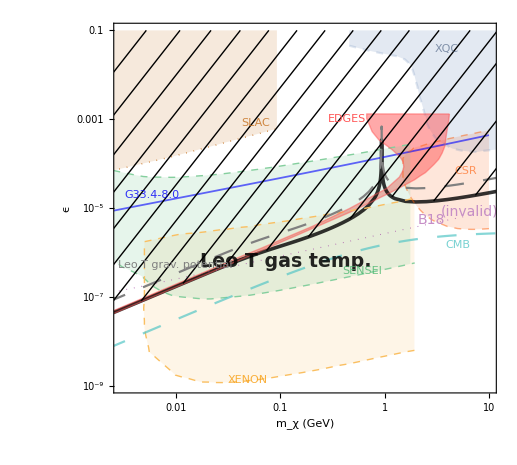

```mathematica
Show[ListLogLogPlot[{ep[1],ep[4],ep[23],ep[12],ep[20],ep[5],ep[11],ep[10],ep[14],ep[16],ep[19],ep[24],ep[21]},Joined->True,AspectRatio->0.9,GridLines->None,GridLinesStyle->Lighter[LightGray],BaseStyle->{FontFamily->"Times",FontSize->15},(*Fill Color & opacity*)Filling->{4->{Top,RGBColor[0.772079, 0.431554, 0.102387, 0.15]},5->{Bottom,{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862, 0.15]}},7->{Top,{RGBColor[0.368417, 0.506779, 0.709798, 0.17]}},8->{{9},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.2]}},10->{Top,{RGBColor[0.9818859269582737, 0.747762968124702, 0.3822413305459943, 0.15]}},12->{{3},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5]}}},FillingStyle->{Opacity[0.3]},PlotStyle->{{GrayLevel[0, 0.8],Thickness->0.005},{RGBColor[0, 0, 1, 0.6],Thickness->0.0025},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],None,Thin},{RGBColor[0.772079, 0.431554, 0.102387],Dotted,Thickness->0.002},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862, 0.49],Dashed,Thin},{Lighter[Purple],Dotted,Thickness->0.0015},{RGBColor[0.368417, 0.506779, 0.709798, 0.2],Dashed},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin},{RGBColor[0.9818859269582737, 0.747762968124702, 0.3822413305459943],Dashed,Thin},{Gray,Dashing[Large]},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],None,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.7000000000000001],Dashing[Large]}},PlotRange->{{0.003,10},{10^-9,10^-1}},Frame->True,FrameLabel->{Style["m_χ (GeV)",18],Style["ϵ",20]},FrameStyle->Black,FrameTicks->{Automatic,Automatic,Automatic,Automatic}],Graphics[{Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,19],Scaled[{0.45,0.355}],{0,0},{2,0.75}],
Text[Style["Leo T grav. potential",Gray],Scaled[{0.16,0.345}],{0,0},{2,0.8}],
Text[Style["CMB",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8]],Scaled[{0.9,0.4}],{0,0},{2,0}],
Text[Style["EDGES",RGBColor[1, Rational[1, 3], Rational[1, 3]]],Scaled[{0.61,0.74}],{0,0},Automatic,{1,0}],
Text[Style["G33.4-8.0",RGBColor[0, 0, 0.98, 0.8]],Scaled[{0.1,0.535}],{0,0},Automatic,{2,0.35}],
Text[Style["SLAC",RGBColor[0.772079, 0.431554, 0.102387, 0.8]],Scaled[{0.37,0.73}],{0,0},Automatic,{1,0.25}],
Text[Style["B18",RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778],14],Scaled[{0.83,0.468}],{0,0},Automatic,{1,0.2}],
Text[Style["(invalid)",RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778],14],Scaled[{0.93,0.49}],{0,0},Automatic,{1,0.2}],
Text[Style["SENSEI",RGBColor[0.28026441037696703, 0.715, 0.4292089322474965, 0.8]],Scaled[{0.65,0.33}],{0,0},Automatic,{1,0.2}],
Text[Style["XENON",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81]],Scaled[{0.35,0.035}],{0,0},Automatic,{1,0.1}],
Text[Style["XQC",RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.6]],Scaled[{0.87,0.93}],{0,0},Automatic,{1,0}],
Text[Style["CSR",RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862, 0.6]],Scaled[{0.92,0.6}],{0,0},Automatic,{1,0}]}],ListLogLogPlot[dashing,PlotRange->{{0.003,10},{10^-9,10^-1}},Joined->True,PlotStyle->{{GrayLevel[0],Thin(*,Thickness->0.00005*)}}]]
```

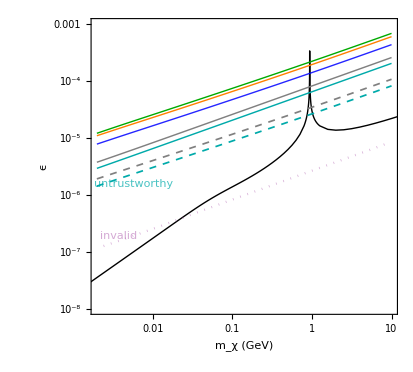

```mathematica
Show[ListLogLogPlot[{ep[1],ep[4],ep[2],ep[3],ep[8],ep[9],ep[17],ep[18],ep[5]},Joined->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->Lighter[LightGray],BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.9,FrameLabel->{Style["m_χ (GeV)",18],Style["ϵ",19]},(*Filling->{1->Top,2->Top,4->Top,7->{8}},*)PlotStyle->{{Black,Thick},{RGBColor[0, 0, 1, 0.85],Thick},{Orange,Thick},{Darker[Green],Thick},{Darker[Cyan],Dashed,Thickness[0.003]},{GrayLevel[0.5],Dashed,Thickness[0.003]},{Darker[Cyan],Thickness[0.0025]},{GrayLevel[0.5],Thickness[0.0025]},{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.5],Dotted,Thickness->0.004}},PlotRange->{{0.002,10},{10^-8,10^-3}}],Graphics[{Text[Style["invalid",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.5]],Scaled[{0.09,0.265}],{0,0},Automatic,{1,0.3}],
Text[Style["untrustworthy",RGBColor[0, Rational[2, 3], Rational[2, 3], 0.7000000000000001]],Scaled[{0.14,0.44}],{0,0},Automatic,{1,0.3}]}]]
```

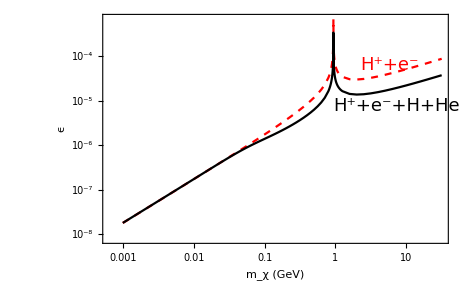

```mathematica
Show[ListLogLogPlot[{ep[22],ep[1]},Joined->True,Frame->True,PlotStyle->{{Red,Dashed},Black},FrameStyle->Black,FrameLabel->{Style["m_χ (GeV)",18],Style["ϵ",20]},GridLines->Automatic,GridLinesStyle->LightGray],Graphics[{Text[Style["H^++e^-+H+He",Black,18],Scaled[{0.85,0.6}],{0,0},{2,0.6}],
Text[Style["H^++e^-",Red,18],Scaled[{0.83,0.78}],{0,0},{2,0.6}]}]]
```

```mathematica
Table[sig10[i]=Import["sigma10/"<>ToString[i]<>".dat"],{i,9}];
Table[p[i]=Import["sigma_p/"<>ToString[i]<>".dat"],{i,16}];
```

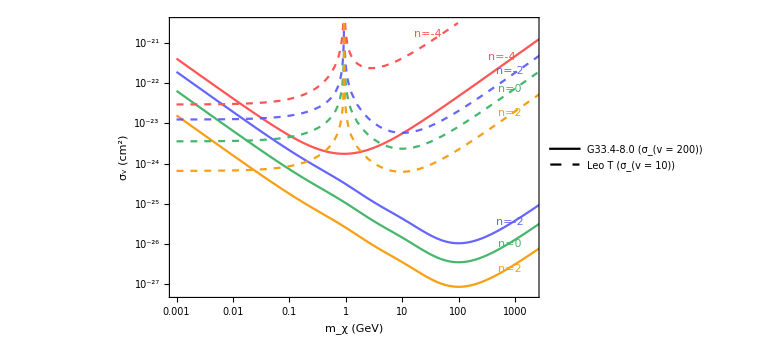

```mathematica
Show[ListLogLogPlot[{p[14],p[15],p[4],p[16],sig10[1],sig10[2],sig10[4],sig10[6]},Joined->True,GridLines->Automatic,GridLinesStyle->Lighter[LightGray],BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,FrameLabel->{Style["m_χ (GeV)",18],Style["σ_v (cm^2)",18]},(*Filling->{1->Top,2->Top,3->Top,4->Top},*)FrameStyle->Black,PlotStyle->{{Lighter[RGBColor[1, 0, 0]]},{Lighter[RGBColor[0, 0, 1, 0.9]]},{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]},{Lighter[RGBColor[1, 0, 0]],Dashed},{Lighter[RGBColor[0, 0, 1, 0.9]],Dashed},{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],Dashed},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],Dashed},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],DotDashed}},PlotRange->{{0.001,2 10^3},{10^-27.2,10^-20.5}},PlotLegends->Placed[LineLegend[{GrayLevel[0],{GrayLevel[0],Dashed}},{"G33.4-8.0 (σ_(v = 200))","Leo T (σ_(v = 10))"},LegendFunction->(Framed[#, FrameMargins-> 1,RoundingRadius->0,FrameStyle->{Gray,Thin}] & ),LegendMargins->2],{0.21,0.1}]],Graphics[{Text[Style["n=-4",Lighter[RGBColor[1, 0, 0]]],Scaled[{0.9,0.86}],{0,0},Automatic,{1,0.6}],
Text[Style["n=-4",Lighter[RGBColor[1, 0, 0]]],Scaled[{0.7,0.94}],{0,0},Automatic,{1,0.5}],
Text[Style["n=-2",Lighter[RGBColor[0, 0, 1, 0.9]]],Scaled[{0.92,0.27}],{0,0},Automatic,{1,0.5}],
Text[Style["n=-2",Lighter[RGBColor[0, 0, 1, 0.9]]],Scaled[{0.92,0.81}],{0,0},Automatic,{1,0.5}],Text[Style["n=0",RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]],Scaled[{0.92,0.19}],{0,0},Automatic,{1,0.5}],
Text[Style["n=0",RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]],Scaled[{0.92,0.745}],{0,0},Automatic,{1,0.5}],
Text[Style["n=2",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]],Scaled[{0.92,0.1}],{0,0},Automatic,{1,0.5}],Text[Style["n=2",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]],Scaled[{0.92,0.66}],{0,0},Automatic,{1,0.5}]}]]
```

```mathematica
Show[ListLogLogPlot[{sig10[4],p[4],p[2],p[3],10^-10 p[7],10^-10 p[8],p[9],p[12],p[13],p[7],p[8]},Joined->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->Lighter[LightGray],BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.9,FrameLabel->{Style["m_χ (GeV)",18],Style["σ_nχ(cm^2)",18]},(*Filling->{1->Top,2->Top,4->Top,7->{8}},*)PlotStyle->{{Black,Thick},{RGBColor[0, 0, 1, 0.85],Thick},{Orange,Thick},{Darker[Green],Thick},{Darker[Cyan],Thickness[0.0025]},{GrayLevel[0.5],Thickness[0.0025]},{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.5],Dotted},{Darker[Cyan],Thickness[0.0025]},{GrayLevel[0.5],Thickness[0.0025]},{Darker[Cyan],Dashed,Thickness[0.003]},{GrayLevel[0.5],Dashed,Thickness[0.003]}},PlotRange->{{0.001,2 10^3},{10^-30,10^-21}},PlotLegends->Placed[{"LeoT","G33.4-8.0","G16.0+3.0","G26.9-6.3","G357.6-4.7-55 (untrustworthy)","G355.3-3.3-118 (untrustworthy)","B18 (invalid)"},{1,0.55}]],Graphics[{Text[Style["invalid",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.7000000000000001]],Scaled[{0.45,0.195}],{0,0},Automatic,{1,-0.6}],
Text[Style["untrustworthy",RGBColor[0, Rational[2, 3], Rational[2, 3], 0.7000000000000001]],Scaled[{0.55,0.3}],{0,0},Automatic,{1,-0.6}]}]]
```

-Graphics-

```mathematica
epInt=Interpolation[Drop[Transpose[{sig10[1][[All,1]],sig10[1][[All,2]](3 10^4)^-4}],-500]];
dashing=Table[{{10^i,epInt[10^i]},{10^(i-3),epInt[10^i] 10^10}},{i,-3,1,0.3}];
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99526} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

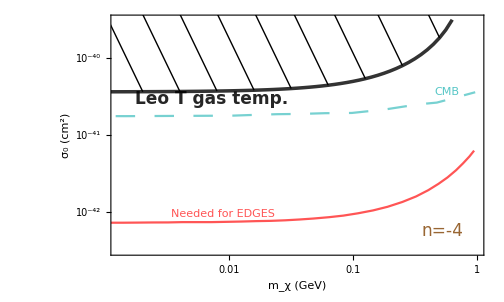

```mathematica
Show[ListLogLogPlot[{Transpose[{sig10[1][[All,1]],sig10[1][[All,2]](3 10^4)^-4}],sig10[7],sig10[8]},AspectRatio->0.6,Joined->True,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,PlotStyle->{{GrayLevel[0, 0.8],Thickness->0.005},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashing[Large]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]}},PlotRange->{{10^-2.9,1},{10^-42.5,10^-39.5}},FrameLabel->{Style["m_χ (GeV)",18],Style["σ_0 (cm^2)",18]},FrameStyle->Black],Graphics[{Brown,Rectangle[{2,1},{4,2}],Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,17],Scaled[{0.27,0.65}],{0,0},{2,0}],
Text[Style["Needed for EDGES",RGBColor[1, Rational[1, 3], Rational[1, 3]]],Scaled[{0.3,0.17}],{0,0},Automatic,{1,0}],Text[Style[Framed["n=-4"],Brown,17],Scaled[{0.89,0.1}],{0,0},Automatic,{1,0}],Text[Style["CMB",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]]],Scaled[{0.9,0.68}],{0,0},{2,0}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin(*,Thickness->0.00005*)}}]]
```

```mathematica
Table[sige[i]=Import["sigma_e/"<>ToString[i]<>".dat"],{i,6}];
```

```mathematica
epInt=Interpolation[Transpose[{sige[1][[All,1]],sige[1][[All,2]]}]];
dashing=Table[{{10^i,epInt[10^i]},{10^(i-3),epInt[10^i] 10^10}},{i,-5.53,1.2,0.3}];
```

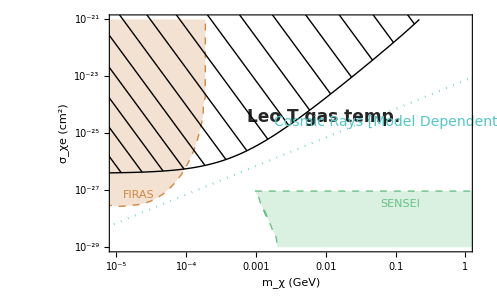

```mathematica
Show[ListLogLogPlot[{sige[1],sige[2],sige[4],sige[5]},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,AspectRatio->0.6,PlotStyle->{{Black,Thick},{RGBColor[0.772079, 0.431554, 0.102387, 0.8],Dashed,Thin},{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965, 0.8],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],Dotted}},PlotRange->{{10^-5,1},{10^-29,10^-21}},Filling->{2->{Top,RGBColor[0.772079, 0.431554, 0.102387, 0.2]},3->{Bottom,RGBColor[0.28026441037696703, 0.715, 0.4292089322474965, 0.2]}},GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},FrameLabel->{Style["m_χ (GeV)",18],Style["σ_χe  (cm^2)",18]}],Graphics[{Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,17],Scaled[{0.59,0.57}],{0,0},Automatic,{1,0.55}],
Text[Style["FIRAS",RGBColor[0.772079, 0.431554, 0.102387, 0.8]],Scaled[{0.08,0.24}],{0,0},Automatic,{1,0.2}],
Text[Style["SENSEI",RGBColor[0.28026441037696703, 0.715, 0.4292089322474965, 0.8]],Scaled[{0.8,0.2}],{0,0},Automatic,{1,0}],
Text[Style["Cosmic Rays [Model Dependent]",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],14],Scaled[{0.77,0.55}],{0,0},Automatic,{1,0.37}]}],
ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin(*,Thickness->0.00005*)}}]]
```